```mathematica
p1=7074;e1=0.05;p2=7748;e2=0.10;d=25000000;a1=2;a2=1;(*p1=a1*(1-e1^2);p2=a2*(1-e2^2);*)
```

```mathematica
nudot[nu_,p_,e_] =Sqrt[1.0/p^3]*(1+e*Cos[nu*3.14/180])^2;
```

```mathematica
nux[nu_,p_,e_]=p/(1+e*Cos[nu*3.14/180])*Cos[nu*3.14/180];
```

```mathematica
nuy[nu_,p_,e_]=p/(1+e*Cos[nu*3.14/180])*Sin[nu*3.14/180];
```

```mathematica
distnu[nu1_,p1_,e1_,nu2_,p2_,e2_]=(nux[nu1,p1,e1]-nux[nu2,p2,e2])^2+(nuy[nu1,p1,e1]-nuy[nu2,p2,e2])^2;
```

```mathematica
(*flow=VectorPlot[{nudot[nu1,a1*(1-e1),e1],nudot[nu2,a2*(1-e2),e2]},{nu1,0,120},{nu2,0,360},VectorPoints->Fine,VectorScale->Tiny];*)
flow=StreamPlot[{nudot[nu1,p1,e1],nudot[nu2,p2,e2]},{nu1,0,360},{nu2,0,360}];
```

```mathematica
rend=RegionPlot[Evaluate[distnu[nu1,p1,e1,nu2,p2,e2]<=d],{nu1,0,360},{nu2,0,360}];
```

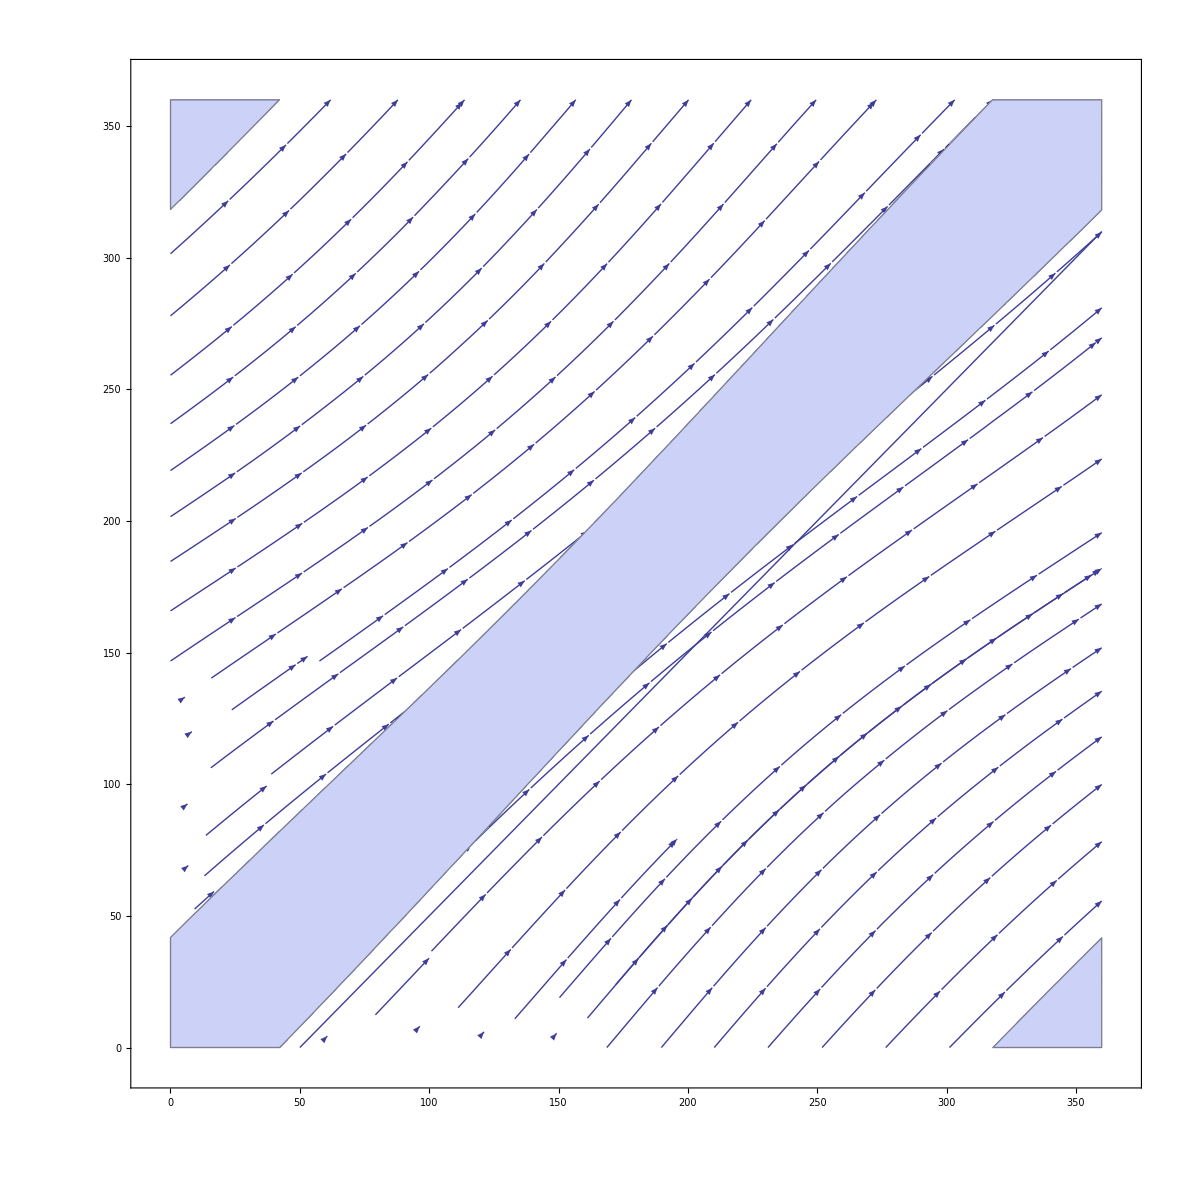

```mathematica
Show[flow,rend,bar]
```

```mathematica
Plot3D[(-7748*Sin[0.0174444444444444*NU2]/(0.1*Cos[0.0174444444444444*NU2]+1)+7074*Sin[0.0174444444444444*NU2]/(0.05*Cos[0.0174444444444444*NU2]+1))*(0.000414815151392623*(0.05*Cos[0.0174444444444444*NU2]+1)*Cos[0.0174444444444444*NU2]-0.000396362293385243*(0.1*Cos[0.0174444444444444*NU2]+1)*Cos[0.0174444444444444*NU2]+2.07407575696311*10^-5*Sin[0.0174444444444444*NU2]^2-3.96362293385243*10^-5*Sin[0.0174444444444444*NU2]^2)+(-7748*Cos[0.0174444444444444*NU2]/(0.1*Cos[0.0174444444444444*NU2]+1)+7074*Cos[0.0174444444444444*NU2]/(0.05*Cos[0.0174444444444444*NU2]+1))*(-0.000414815151392623*(0.05*Cos[0.0174444444444444*NU2]+1)*Sin[0.0174444444444444*NU2]+0.000396362293385243*(0.1*Cos[0.0174444444444444*NU2]+1)*Sin[0.0174444444444444*NU2]+2.07407575696311*10^-5*Sin[0.0174444444444444*NU2]*Cos[0.0174444444444444*NU2]-3.96362293385243*10^-5*Sin[0.0174444444444444*NU2]*Cos[0.0174444444444444*NU2]),{NU1,200,250},{NU2,100,13
0}]
```

-Graphics3D-

```mathematica
FullSimplify[(-7748*Sin[0.0174444444444444*NU2]/(0.1*Cos[0.0174444444444444*NU2]+1)+7074*Sin[0.0174444444444444*NU2]/(0.05*Cos[0.0174444444444444*NU2]+1))*(0.000414815151392623*(0.05*Cos[0.0174444444444444*NU2]+1)*Cos[0.0174444444444444*NU2]-0.000396362293385243*(0.1*Cos[0.0174444444444444*NU2]+1)*Cos[0.0174444444444444*NU2]+2.07407575696311*10^-5*Sin[0.0174444444444444*NU2]^2-3.96362293385243*10^-5*Sin[0.0174444444444444*NU2]^2)+(-7748*Cos[0.0174444444444444*NU2]/(0.1*Cos[0.0174444444444444*NU2]+1)+7074*Cos[0.0174444444444444*NU2]/(0.05*Cos[0.0174444444444444*NU2]+1))*(-0.000414815151392623*(0.05*Cos[0.0174444444444444*NU2]+1)*Sin[0.0174444444444444*NU2]+0.000396362293385243*(0.1*Cos[0.0174444444444444*NU2]+1)*Sin[0.0174444444444444*NU2]+2.07407575696311*10^-5*Sin[0.0174444444444444*NU2]*Cos[0.0174444444444444*NU2]-3.96362293385243*10^-5*Sin[0.0174444444444444*NU2]*Cos[0.0174444444444444*NU2])]
```

((2.54711-1.20931 Cos[0.0174444 NU2]) Sin[0.0174444 NU2])/(200.5+30. Cos[0.0174444 NU2]+0.5 Cos[0.0348889 NU2])

```mathematica
%//FortranForm
```

((2.547109594446804 - 1.209310193209165*Cos(0.0174444444444444*NU2))*Sin(0.0174444444444444*NU2))/(200.5 + 30.*Cos(0.0174444444444444*NU2) + 0.5*Cos(0.0348888888888888*NU2))

```mathematica
((-7748*Sin(0.0174444444444444*NU2)/(0.1*Cos(0.0174444444444444*NU2)+1)+7074*sin(0.0174444444444444*NU1)/(0.05*cos(0.0174444444444444*NU1)+1))*(0.000414815151392623*(0.05*cos(0.0174444444444444*NU1)+1)*cos(0.0174444444444444*NU1)-0.000396362293385243*(0.1*cos(0.0174444444444444*NU2)+1)*cos(0.0174444444444444*NU2)+2.07407575696311*10^-5*sin(0.0174444444444444*NU1)^2-3.96362293385243*10^-5*sin(0.0174444444444444*NU2)^2)+(-7748*cos(0.0174444444444444*NU2)/(0.1*cos(0.0174444444444444*NU2)+1)+7074*cos(0.0174444444444444*NU1)/(0.05*cos(0.0174444444444444*NU1)+1))*(-0.000414815151392623*(0.05*cos(0.0174444444444444*NU1)+1)*sin(0.0174444444444444*NU1)+0.000396362293385243*(0.1*cos(0.0174444444444444*NU2)+1)*sin(0.0174444444444444*NU2)+2.07407575696311*10^-5*sin(0.0174444444444444*NU1)*cos(0.0174444444444444*NU1)-3.96362293385243*10^-5*sin(0.0174444444444444*NU2)*cos(0.0174444444444444*NU2))>0
```

(-54.7719820123898*Sin(0.0174*NU1) - 28.0386689048304*Sin(0.0174*NU1 - 0.0348888888888889*NU2) + 79.9555045189646*Sin(0.0174*NU1 - 0.0174*NU2) + 16.0699389712652*Sin(0.0348888888888889*NU1 - 0.0174*NU2) - 
     -    0.6046550881563859*Sin(0.0174*NU1 + 0.0174*NU2) + 13.21048368224364*Sin(0.0174*NU2))/((20.000000000000004 + 1.*Cos(0.0174*NU1))*(10. + 1.*Cos(0.0174*NU2)))

```mathematica
FullSimplify[Expand[distnu[nu1,p1,e1,nu2,p2,e2]]]
```

(4.41045×10^12+2.08886×10^10 Cos[0.0174444 nu1]-2.47936×10^9 Cos[0.0348889 nu1]-2.19237×10^11 Cos[0.0174444 nu1-0.0348889 nu2]-5.48094×10^9 Cos[0.0348889 nu1-0.0348889 nu2]-4.38475×10^12 Cos[0.0174444 nu1-0.0174444 nu2]-1.09619×10^11 Cos[0.0348889 nu1-0.0174444 nu2]+2.90713×10^11 Cos[0.0174444 nu2]+4.52736×10^9 Cos[0.0348889 nu2])/((20.+1. Cos[0.0174444 nu1])^2 (10.+1. Cos[0.0174444 nu2])^2)